## Going through, taking out all $SSS... globals, putting them into an <||>

#### TestSSSAssoc.0.nb failed because for some reason doing the substitution Last[ans["TEvolution"]] /. ans["TRuleSet"] does not correctly perform the needed side jobs, such as incrementing ans["TagIndex"].

#### In TestSSSAssoc.1.nb I'm reverting to using a few of the $SSS... globals in SSSNewRule (and consequently in the tagged ruleset), but in both SSSInitialize and SSSSingleStep I'll load and unload the globals from the association values, so no need to worry about them.

#### Everything works now. But it would be good to change SSSSingleStep and SSSEvolve to act on their first argument (the SSS) rather than having to return a new object. To implement pass by reference, use the Attribute HoldFirst.

```mathematica
Clear[FromAlpha,ToAlpha,SSSConvert,SSSStrip];
FromAlpha[string_String] :=(ToCharacterCode[string]-65);  
ToAlpha[l:{___Integer}] := FromCharacterCode[l+65];

Attributes[s]=Flat;
SSSConvert[string_String] := s @@ FromAlpha[string];
SSSConvert[s[x___]] := ToAlpha[{x}];
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats, using the functions FromAlpha and ToAlpha.";

SSSStrip[x_s] := SSSConvert[x⟦All,1⟧] /; MatrixQ[List@@x]    (* if dim=2, take only 1st component, and convert *)
SSSStrip[x_s] := ""  /; Length[List@@x]==0     (* treat empty string case *) 

SSSStrip::usage="SSSStrip[StyleBox[\"state\",FontSlant->\"Italic\"]] strips out tags from a StyleBox[\"state\",FontSlant->\"Italic\"] given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
ToCharacterWeights[s_String] := (1+FromAlpha[s]);
FromCharacterWeights[l:{___Integer}] := ToAlpha[l-1];
(* Note: To avoid breaking the ruleset (un-)rank functions, avoid the temptation to define:  
ToCharacterWeights[""] = 0;  FromCharacterWeights[{0}]="";  *)
StringWeight[s_String] := Plus @@ ToCharacterWeights[s];
RuleSetWeight[rs_List] := Plus @@ (StringWeight /@ Flatten[rs /. Rule->List]);
RuleSetLength[rs_List] := Plus @@ (StringLength /@ Flatten[rs /. Rule->List]);
```

$MaxColor = 6;

(1) Just remove $MaxColor.  
(2) Add maxColor parameter to myColors, patternPrint, SSSRuleIcon).

Come back and work this through more carefully later.

```mathematica
Clear[myColors,myColorOptions,patternPrint,SSSRuleIcon]
```

```mathematica
myColorOptions[maxColor_Integer]:=Sequence[ColorRules->{0->LightGray},ColorFunction->(Hue[(#-1)/maxColor]&),ColorFunctionScaling->False];
```

```mathematica
patternPrint[pattern_,mxClr_Integer,opts___] := ArrayPlot[{{##}}& @@pattern,myColorOptions[mxClr],Mesh->True,opts,ImageSize->{Automatic,20}];
```

```mathematica
Clear[SSSRuleIcon];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,mxClr_Integer:6,opts___] := Panel[Grid[Map[patternPrint[#,mxClr,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
```

```mathematica
SSSRuleIcon::usage="SSSRuleIcon[rule(s),maxColor] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```


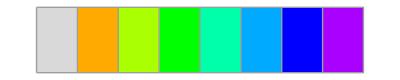
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ACDEFGHI"},9]
```

```mathematica
SSSNewRule[rulenum_Integer,(rule_Rule | rule_RuleDelayed)] := 
(* the tagged rule created will need valid versions of $SSSConnectionList, $SSSTagIndex, $SSSRulesUsed, and will change them!  It's up to the calling routine to load/unload these globals.  *)
Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@Transpose[{FromAlpha[lhs],ToString@#<>"_"& /@ lhsNames}]];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2=ToString[SSSConvert[rhs] /. n_Integer :> {n,"$SSSTagIndex++"}];
ToExpression[newlhs<>" :> ("<>"AppendTo[$SSSRulesUsed,"<>ToString@rulenum<>"];"<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := Append[MapIndexed[SSSNewRule[First[#2],#1]&,rules],___:>AppendTo[$SSSRulesUsed,0]];
SSSNewRule::usage= 
"SSSNewRule[rule(s)] generates the needed rules for the tagged SSS (sequential substitution system) from the ruleset of rules given in string-format: e.g., \"BA\"→\"ABA\"";
```

```mathematica
SSSNewRule[{"ABA"->"AAB","A"->"ABA"}]
```

```mathematica
Clear[SSSInitialize];
Options[SSSInitialize]={Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSInitialize::usage = "StyleBox[\"variable\",FontSlant->\"Italic\"] = SSSInitialize[ruleset, string, (mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,\nstarting with a ruleset (e.g., {\"BA\"→\"ABA\"}) and an initial state string (e.g., \"BABA\").  The True|False return value indicates whether initialization was successful.\n\nIf omitted, mode defaults to \"Silent\", suppressing the short error or success message.\n\nThe following global variables are reset by this operation:\n\n$SSSNet:\t\t\t\tthe causal network of the current SSS,\n$SSSInDegree:\t\t\tthe list of in-degrees for each node,\n$SSSOutDegreeActual:\t\tthe list of currently found out-degrees for each node,\n$SSSOutDegreePotential:\t\tthe list of maximum possible out-degrees for each node,\n$SSSOutDegreeRemaining:\tthe list of numbers of possible remaining out-connections for each node,\n$SSSConnectionList:\t\tthe current list of all causal network connections,\n$SSSDistance:\t\t\tthe list of minimum distances from the current node back to the starting node.\n$SSSTagIndex:\t\t\tthe current tag index being used,\n$SSSTEvolution:\t\t\tthe complete evolution of the tagged SSS so far,\n$SSSEvolution:\t\t\tthe stripped (tagless) version of $SSSTEvolution,\n$SSSRuleSet:\t\t\tthe ruleset used for creating the SSS,\n$SSSTRuleSet:\t\t\tthe version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,\n$SSSRuleSetWeight:\t\tthe total weight of $SSSRuleSet,\n$SSSRuleSetLength:\t\tthe total length of $SSSRuleSet,\n$SSSRulesUsed:\t\tthe list of rules used\n$SSSCellsDeleted:\t\tthe list of cells in the state string deleted at each step,\n$SSSVerdict:\t\t\tset to \"Dead\" | \"Repeating\" as soon as the future of the SSS becomes clear.";

SSSInitialize[rs:{___Rule},state_String,opts:OptionsPattern[] (* Mode -> Silent | Quiet | Loud *)] :=
Module[{ans=<|"Net"->{},"OutDegreePotential"->{},"OutDegreeRemaining"->{},"OutDegreeActual"-> {},
"InDegree"-> {},"ConnectionList"->{},"Verdict"->"OK", "RulesUsed"->{},"CellsDeleted"->{},
"Distance"->{0}|>}, (* initial setup *)
AssociateTo[ans,{
"MaxColor"->Max[Flatten[{6,ToCharacterWeights /@ Flatten[rs/.Rule->List]}]],
"TagIndex"->StringLength[state]+1,
"TEvolution"->{s@@Transpose[{#,Range[Length[#]]}& @ FromAlpha[state]]},
"Evolution"->{state}, "RuleSet"->rs, "TRuleSet"->SSSNewRule[rs],
"RuleSetWeight"->RuleSetWeight[rs], "RuleSetLength"->RuleSetLength[rs]
}];

{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

Switch[ Last[ans["RulesUsed"]], (* can also test if Length[ans["ConnectionList"]]==0 *)
0,ans["TEvolution"]=Most[ans["TEvolution"]]; (* toss last duplicate entry *)
      ans["Verdict"]="Dead";
      If[ OptionValue[Mode]==Loud,Print["Error: No evolution possible starting from \""<>state<>"\" using ruleset: ",rs]];
      Return[ans (* but already including "Verdict" = Dead *)],
_, AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]]; (* add last entry *)
       If[ OptionValue[Mode]==Loud,Print["Successful initialization of ruleset: ",rs,", evolution: ",ans["Evolution"]]]
];
(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; (* # of cells created by last rule *)
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

ans  (* Return the association created *)
];
```

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A"];
```

```mathematica
Normal[sss]//Column
```

Net→{}
OutDegreePotential→{3}
OutDegreeRemaining→{3}
OutDegreeActual→{0}
InDegree→{1}
ConnectionList→{{1}→{2,3,4}}
Verdict→OK
RulesUsed→{2}
CellsDeleted→{{1}}
Distance→{0}
MaxColor→6
TagIndex→5
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}]}
Evolution→{A,ABA}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$3512_},{1,lhsTag$3513_},{0,lhsTag$3514_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$3512,lhsTag$3513,lhsTag$3514}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$3516_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$3516}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
{sss["TagIndex"],sss["Evolution"]}
```

{5,{A,ABA}}

```mathematica
Clear[SSSSingleStep];

SSSSingleStep::usage=
"SSSSingleStep[sss] performs a single step of the sequential substitution system sss evolution (if not already dead), returning the sss object (which must be created by SSSInitialize first).";

SSSSingleStep[sss_Association] := Module[{ans=sss,cd, ri, pri, rs, prs,len,startingEvents, oda, odr},
If[ans["Verdict"]==="Dead",Return[ans]];  (* if already dead, do nothing, return *)

(* do the actual evolution step *)
{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

If[Last[ans["RulesUsed"]]==0,ans["Verdict"]="Dead"; 
ans["TEvolution"]=Most[ans["TEvolution"]]; 
Return[ans]
];

AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]];

If[!MatchQ[ans["Verdict"],"Repeating"],  (* to limit wasted time, don't do this if the verdict is already in! *)
If[Length[Flatten@Position[ans["Evolution"],Last[ans["Evolution"]]]]>1, ans["Verdict"]="Repeating"]
]; 

(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; 
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

(* now the steps that are only done for non-initial steps, comparing to previous entries in ans["ConnectionList"]: *)
len=Length[ans["ConnectionList"]];
startingEvents=Flatten[If[Length[#]>0,First[First[#]],#]& /@ (Position[ans["ConnectionList"]⟦;;-2⟧,#]& /@ ans["ConnectionList"]⟦-1,1⟧)];
oda=ans["OutDegreeActual"];
oda⟦#⟧++& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeActual"->oda];
odr=ans["OutDegreeRemaining"];
odr⟦#⟧--& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeRemaining"->odr];
AssociateTo[ans,"Net"->Join[ans["Net"],#->len& /@ startingEvents]];           (* add new links to the causal network *)
AssociateTo[ans,"Distance"->Append[ans["Distance"],Min[ans["Distance"]⟦startingEvents⟧]+1]];  (* Find minimum path length of cause nodes, add 1 for path lengths of result nodes *)

ans  (* Return the updated association *)
];
```

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A"];
Normal[sss]//Column
```

Net→{}
OutDegreePotential→{3}
OutDegreeRemaining→{3}
OutDegreeActual→{0}
InDegree→{1}
ConnectionList→{{1}→{2,3,4}}
Verdict→OK
RulesUsed→{2}
CellsDeleted→{{1}}
Distance→{0}
MaxColor→6
TagIndex→5
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}]}
Evolution→{A,ABA}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$15508_},{1,lhsTag$15509_},{0,lhsTag$15510_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$15508,lhsTag$15509,lhsTag$15510}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$15512_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$15512}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
sss=SSSSingleStep[sss];
Normal[sss]//Column
```

Net→{1→2,1→2,1→2}
OutDegreePotential→{3,3}
OutDegreeRemaining→{0,3}
OutDegreeActual→{3,0}
InDegree→{1,3}
ConnectionList→{{1}→{2,3,4},{2,3,4}→{5,6,7}}
Verdict→OK
RulesUsed→{2,1}
CellsDeleted→{{1},{1,2,3}}
Distance→{0,1}
MaxColor→6
TagIndex→8
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}],s[{0,5},{0,6},{1,7}]}
Evolution→{A,ABA,AAB}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$15508_},{1,lhsTag$15509_},{0,lhsTag$15510_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$15508,lhsTag$15509,lhsTag$15510}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$15512_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$15512}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
Clear[SSSEvolve];
Options[SSSEvolve]={EarlyReturn->False, Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSEvolve[sss_Association,n_Integer/;n>0,opts:OptionsPattern[]] := Module[{ans=sss},
If[OptionValue[EarlyReturn] ,
Do[If[MatchQ[ans["Verdict"], ("Dead"|"Repeating")],Return[ans],ans=SSSSingleStep[ans]],{n}], (* check before each step *)
Do[ans=SSSSingleStep[ans],{n}]   (* just do it *)
];
If[OptionValue[Mode]==Loud,Print[ans["Verdict"]]];
ans
]
```

```mathematica
SSSEvolve::usage="SSSEvolve[sss, n] generates an additional n levels of indicated sss (sequential substitution system), which must have been previously created using SSSInitialize.  Use the option EarlyReturn → True to allow early termination for repeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.)  In Loud mode, prints the current verdict, \"OK\" means none known.  Values of sss updated, with \"Evolution\" containing the tagless SSS, \"ConnectionList\" the updated causal network connection list, etc.  mode can be Silent, Quiet, or Loud.";
```

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A"];
Normal[sss]//Column
```

Net→{}
OutDegreePotential→{3}
OutDegreeRemaining→{3}
OutDegreeActual→{0}
InDegree→{1}
ConnectionList→{{1}→{2,3,4}}
Verdict→OK
RulesUsed→{2}
CellsDeleted→{{1}}
Distance→{0}
MaxColor→6
TagIndex→5
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}]}
Evolution→{A,ABA}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$16567_},{1,lhsTag$16568_},{0,lhsTag$16569_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$16567,lhsTag$16568,lhsTag$16569}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$16571_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$16571}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
sss=SSSEvolve[sss,50];
Normal[sss]//Column
```

Net→{1→2,1→2,1→2,2→3,3→4,3→4,3→4,4→5,4→5,2→5,4→6,6→7,6→7,6→7,7→8,7→8,5→8,8→9,8→9,5→9,7→10,10→11,10→11,10→11,11→12,11→12,8→12,12→13,12→13,9→13,13→14,13→14,9→14,11→15,15→16,15→16,15→16,16→17,16→17,12→17,17→18,17→18,13→18,18→19,18→19,14→19,19→20,19→20,14→20,16→21,21→22,21→22,21→22,22→23,22→23,17→23,23→24,23→24,18→24,24→25,24→25,19→25,25→26,25→26,20→26,26→27,26→27,20→27,22→28,28→29,28→29,28→29,29→30,29→30,23→30,30→31,30→31,24→31,31→32,31→32,25→32,32→33,32→33,26→33,33→34,33→34,27→34,34→35,34→35,27→35,29→36,36→37,36→37,36→37,37→38,37→38,30→38,38→39,38→39,31→39,39→40,39→40,32→40,40→41,40→41,33→41,41→42,41→42,34→42,42→43,42→43,35→43,43→44,43→44,35→44,37→45,45→46,45→46,45→46,46→47,46→47,38→47,47→48,47→48,39→48,48→49,48→49,40→49,49→50,49→50,41→50,50→51,50→51,42→51,51→52,51→52,43→52,52→53,52→53,44→53,53→54,53→54,44→54,46→55,55→56,55→56,55→56,56→57,56→57,47→57,57→58,57→58,48→58,58→59,58→59,49→59,59→60,59→60,50→60,60→61,60→61,51→61,61→62,61→62,52→62,62→63,62→63,53→63,63→64,63→64,54→64,64→65,64→65,54→65,56→66,66→67,66→67,66→67,67→68,67→68,57→68,68→69,68→69,58→69,69→70,69→70,59→70,70→71,70→71,60→71,71→72,71→72,61→72,72→73,72→73,62→73,73→74,73→74,63→74,74→75,74→75,64→75,75→76,75→76,65→76,76→77,76→77,65→77,67→78,78→79,78→79,78→79,79→80,79→80,68→80,80→81,80→81,69→81,81→82,81→82,70→82,82→83,82→83,71→83,83→84,83→84,72→84,84→85,84→85,73→85,85→86,85→86,74→86,86→87,86→87,75→87,87→88,87→88,76→88,88→89,88→89,77→89,89→90,89→90,77→90,79→91,91→92,91→92,91→92,92→93,92→93,80→93,93→94,93→94,81→94,94→95,94→95,82→95,95→96,95→96,83→96,96→97,96→97,84→97,97→98,97→98,85→98,98→99,98→99,86→99,99→100,99→100,87→100,100→101,100→101,88→101}
OutDegreePotential→{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
OutDegreeRemaining→{0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,3,0,1,1,1,1,1,1,1,1,1,3}
OutDegreeActual→{3,2,3,3,2,3,3,3,2,3,3,3,3,2,3,3,3,3,3,2,3,3,3,3,3,3,2,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,2,0,3,2,2,2,2,2,2,2,2,2,0}
InDegree→{1,3,1,3,3,1,3,3,3,1,3,3,3,3,1,3,3,3,3,3,1,3,3,3,3,3,3,1,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3,3,3}
ConnectionList→{{1}→{2,3,4},{2,3,4}→{5,6,7},{5}→{8,9,10},{8,9,10}→{11,12,13},{12,13,6}→{14,15,16},{11}→{17,18,19},{17,18,19}→{20,21,22},{21,22,14}→{23,24,25},{24,25,15}→{26,27,28},{20}→{29,30,31},{29,30,31}→{32,33,34},{33,34,23}→{35,36,37},{36,37,26}→{38,39,40},{39,40,27}→{41,42,43},{32}→{44,45,46},{44,45,46}→{47,48,49},{48,49,35}→{50,51,52},{51,52,38}→{53,54,55},{54,55,41}→{56,57,58},{57,58,42}→{59,60,61},{47}→{62,63,64},{62,63,64}→{65,66,67},{66,67,50}→{68,69,70},{69,70,53}→{71,72,73},{72,73,56}→{74,75,76},{75,76,59}→{77,78,79},{78,79,60}→{80,81,82},{65}→{83,84,85},{83,84,85}→{86,87,88},{87,88,68}→{89,90,91},{90,91,71}→{92,93,94},{93,94,74}→{95,96,97},{96,97,77}→{98,99,100},{99,100,80}→{101,102,103},{102,103,81}→{104,105,106},{86}→{107,108,109},{107,108,109}→{110,111,112},{111,112,89}→{113,114,115},{114,115,92}→{116,117,118},{117,118,95}→{119,120,121},{120,121,98}→{122,123,124},{123,124,101}→{125,126,127},{126,127,104}→{128,129,130},{129,130,105}→{131,132,133},{110}→{134,135,136},{134,135,136}→{137,138,139},{138,139,113}→{140,141,142},{141,142,116}→{143,144,145},{144,145,119}→{146,147,148},{147,148,122}→{149,150,151},{150,151,125}→{152,153,154},{153,154,128}→{155,156,157},{156,157,131}→{158,159,160},{159,160,132}→{161,162,163},{137}→{164,165,166},{164,165,166}→{167,168,169},{168,169,140}→{170,171,172},{171,172,143}→{173,174,175},{174,175,146}→{176,177,178},{177,178,149}→{179,180,181},{180,181,152}→{182,183,184},{183,184,155}→{185,186,187},{186,187,158}→{188,189,190},{189,190,161}→{191,192,193},{192,193,162}→{194,195,196},{167}→{197,198,199},{197,198,199}→{200,201,202},{201,202,170}→{203,204,205},{204,205,173}→{206,207,208},{207,208,176}→{209,210,211},{210,211,179}→{212,213,214},{213,214,182}→{215,216,217},{216,217,185}→{218,219,220},{219,220,188}→{221,222,223},{222,223,191}→{224,225,226},{225,226,194}→{227,228,229},{228,229,195}→{230,231,232},{200}→{233,234,235},{233,234,235}→{236,237,238},{237,238,203}→{239,240,241},{240,241,206}→{242,243,244},{243,244,209}→{245,246,247},{246,247,212}→{248,249,250},{249,250,215}→{251,252,253},{252,253,218}→{254,255,256},{255,256,221}→{257,258,259},{258,259,224}→{260,261,262},{261,262,227}→{263,264,265},{264,265,230}→{266,267,268},{267,268,231}→{269,270,271},{236}→{272,273,274},{272,273,274}→{275,276,277},{276,277,239}→{278,279,280},{279,280,242}→{281,282,283},{282,283,245}→{284,285,286},{285,286,248}→{287,288,289},{288,289,251}→{290,291,292},{291,292,254}→{293,294,295},{294,295,257}→{296,297,298},{297,298,260}→{299,300,301},{300,301,263}→{302,303,304}}
Verdict→OK
RulesUsed→{2,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1}
CellsDeleted→{{1},{1,2,3},{1},{1,2,3},{2,3,4},{1},{1,2,3},{2,3,4},{3,4,5},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12},{11,12,13},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12},{11,12,13},{12,13,14},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11},{10,11,12}}
Distance→{0,1,2,3,2,4,5,3,3,6,7,4,4,4,8,9,5,5,5,5,10,11,6,6,6,6,6,12,13,7,7,7,7,7,7,14,15,8,8,8,8,8,8,8,16,17,9,9,9,9,9,9,9,9,18,19,10,10,10,10,10,10,10,10,10,20,21,11,11,11,11,11,11,11,11,11,11,22,23,12,12,12,12,12,12,12,12,12,12,12,24,25,13,13,13,13,13,13,13,13,13}
MaxColor→6
TagIndex→305
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}],s[{0,5},{0,6},{1,7}],s[{0,8},{1,9},{0,10},{0,6},{1,7}],s[{0,11},{0,12},{1,13},{0,6},{1,7}],s[{0,11},{0,14},{0,15},{1,16},{1,7}],s[{0,17},{1,18},{0,19},{0,14},{0,15},{1,16},{1,7}],s[{0,20},{0,21},{1,22},{0,14},{0,15},{1,16},{1,7}],s[{0,20},{0,23},{0,24},{1,25},{0,15},{1,16},{1,7}],s[{0,20},{0,23},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,29},{1,30},{0,31},{0,23},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,33},{1,34},{0,23},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,35},{0,36},{1,37},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,35},{0,38},{0,39},{1,40},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,35},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,44},{1,45},{0,46},{0,35},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,48},{1,49},{0,35},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,51},{1,52},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,53},{0,54},{1,55},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,53},{0,56},{0,57},{1,58},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,62},{1,63},{0,64},{0,50},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,66},{1,67},{0,50},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,69},{1,70},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,72},{1,73},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,74},{0,75},{1,76},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,74},{0,77},{0,78},{1,79},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,83},{1,84},{0,85},{0,68},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,87},{1,88},{0,68},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,90},{1,91},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,93},{1,94},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,96},{1,97},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,98},{0,99},{1,100},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,98},{0,101},{0,102},{1,103},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,107},{1,108},{0,109},{0,89},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,111},{1,112},{0,89},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,114},{1,115},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,117},{1,118},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,120},{1,121},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,123},{1,124},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,125},{0,126},{1,127},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,125},{0,128},{0,129},{1,130},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,134},{1,135},{0,136},{0,113},{0,116},{0,119},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,138},{1,139},{0,113},{0,116},{0,119},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,141},{1,142},{0,116},{0,119},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,144},{1,145},{0,119},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,146},{0,147},{1,148},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,146},{0,149},{0,150},{1,151},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,146},{0,149},{0,152},{0,153},{1,154},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,146},{0,149},{0,152},{0,155},{0,156},{1,157},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,146},{0,149},{0,152},{0,155},{0,158},{0,159},{1,160},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,137},{0,140},{0,143},{0,146},{0,149},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,164},{1,165},{0,166},{0,140},{0,143},{0,146},{0,149},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,168},{1,169},{0,140},{0,143},{0,146},{0,149},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,171},{1,172},{0,143},{0,146},{0,149},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,174},{1,175},{0,146},{0,149},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,177},{1,178},{0,149},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,179},{0,180},{1,181},{0,152},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,179},{0,182},{0,183},{1,184},{0,155},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,179},{0,182},{0,185},{0,186},{1,187},{0,158},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,179},{0,182},{0,185},{0,188},{0,189},{1,190},{0,161},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,179},{0,182},{0,185},{0,188},{0,191},{0,192},{1,193},{0,162},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,167},{0,170},{0,173},{0,176},{0,179},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,197},{1,198},{0,199},{0,170},{0,173},{0,176},{0,179},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,201},{1,202},{0,170},{0,173},{0,176},{0,179},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,204},{1,205},{0,173},{0,176},{0,179},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,207},{1,208},{0,176},{0,179},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,210},{1,211},{0,179},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,213},{1,214},{0,182},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,215},{0,216},{1,217},{0,185},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,219},{1,220},{0,188},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,222},{1,223},{0,191},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,225},{1,226},{0,194},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,228},{1,229},{0,195},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,200},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,233},{1,234},{0,235},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,237},{1,238},{0,203},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,240},{1,241},{0,206},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,243},{1,244},{0,209},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,246},{1,247},{0,212},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,249},{1,250},{0,215},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,252},{1,253},{0,218},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,255},{1,256},{0,221},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,258},{1,259},{0,224},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,261},{1,262},{0,227},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,264},{1,265},{0,230},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,267},{1,268},{0,231},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,236},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,272},{1,273},{0,274},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,276},{1,277},{0,239},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,279},{1,280},{0,242},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,282},{1,283},{0,245},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,285},{1,286},{0,248},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,287},{0,288},{1,289},{0,251},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,287},{0,290},{0,291},{1,292},{0,254},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,287},{0,290},{0,293},{0,294},{1,295},{0,257},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,287},{0,290},{0,293},{0,296},{0,297},{1,298},{0,260},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,287},{0,290},{0,293},{0,296},{0,299},{0,300},{1,301},{0,263},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,275},{0,278},{0,281},{0,284},{0,287},{0,290},{0,293},{0,296},{0,299},{0,302},{0,303},{1,304},{0,266},{0,269},{0,270},{1,271},{1,232},{1,196},{1,163},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}]}
Evolution→{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB,ABAAAAAAAAABBBBBBBB,AABAAAAAAAABBBBBBBB,AAABAAAAAAABBBBBBBB,AAAABAAAAAABBBBBBBB,AAAAABAAAAABBBBBBBB,AAAAAABAAAABBBBBBBB,AAAAAAABAAABBBBBBBB,AAAAAAAABAABBBBBBBB,AAAAAAAAABABBBBBBBB,AAAAAAAAAABBBBBBBBB,ABAAAAAAAAAABBBBBBBBB,AABAAAAAAAAABBBBBBBBB,AAABAAAAAAAABBBBBBBBB,AAAABAAAAAAABBBBBBBBB,AAAAABAAAAAABBBBBBBBB,AAAAAABAAAAABBBBBBBBB,AAAAAAABAAAABBBBBBBBB,AAAAAAAABAAABBBBBBBBB,AAAAAAAAABAABBBBBBBBB,AAAAAAAAAABABBBBBBBBB,AAAAAAAAAAABBBBBBBBBB,ABAAAAAAAAAAABBBBBBBBBB,AABAAAAAAAAAABBBBBBBBBB,AAABAAAAAAAAABBBBBBBBBB,AAAABAAAAAAAABBBBBBBBBB,AAAAABAAAAAAABBBBBBBBBB,AAAAAABAAAAAABBBBBBBBBB,AAAAAAABAAAAABBBBBBBBBB,AAAAAAAABAAAABBBBBBBBBB,AAAAAAAAABAAABBBBBBBBBB,AAAAAAAAAABAABBBBBBBBBB,AAAAAAAAAAABABBBBBBBBBB,AAAAAAAAAAAABBBBBBBBBBB,ABAAAAAAAAAAAABBBBBBBBBBB,AABAAAAAAAAAAABBBBBBBBBBB,AAABAAAAAAAAAABBBBBBBBBBB,AAAABAAAAAAAAABBBBBBBBBBB,AAAAABAAAAAAAABBBBBBBBBBB,AAAAAABAAAAAAABBBBBBBBBBB,AAAAAAABAAAAAABBBBBBBBBBB,AAAAAAAABAAAAABBBBBBBBBBB,AAAAAAAAABAAAABBBBBBBBBBB,AAAAAAAAAABAAABBBBBBBBBBB,AAAAAAAAAAABAABBBBBBBBBBB,AAAAAAAAAAAABABBBBBBBBBBB,AAAAAAAAAAAAABBBBBBBBBBBB,ABAAAAAAAAAAAAABBBBBBBBBBBB,AABAAAAAAAAAAAABBBBBBBBBBBB,AAABAAAAAAAAAAABBBBBBBBBBBB,AAAABAAAAAAAAAABBBBBBBBBBBB,AAAAABAAAAAAAAABBBBBBBBBBBB,AAAAAABAAAAAAAABBBBBBBBBBBB,AAAAAAABAAAAAAABBBBBBBBBBBB,AAAAAAAABAAAAAABBBBBBBBBBBB,AAAAAAAAABAAAAABBBBBBBBBBBB,AAAAAAAAAABAAAABBBBBBBBBBBB,AAAAAAAAAAABAAABBBBBBBBBBBB}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$16567_},{1,lhsTag$16568_},{0,lhsTag$16569_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$16567,lhsTag$16568,lhsTag$16569}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$16571_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$16571}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
Clear[SSSDisplay];
Options[SSSDisplay]=
{HighlightMethod->True,RulePlacement->Bottom,Mesh->True,NetSize->{Automatic,400},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,
Max->∞,SSSMax->Automatic,NetMax->Automatic,
Min->1,SSSMin->Automatic,NetMin->Automatic, 
Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
SyntaxInformation[SSSDisplay]={"ArgumentsPattern"->{OptionsPattern[]}};
```

```mathematica
SSSDisplay[sss_Association, opts:OptionsPattern[]] := Module[{HlM,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,mn,netmn,sssmn,hs,start,ev,vrtxs,net,grph,DE},

HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
RP=OptionValue[RulePlacement];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
DE= OptionValue[DirectedEdges];

mx=OptionValue[Max];
If[mx===Automatic,mx=∞];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];

mn=OptionValue[Min];
If[mn===Automatic,mn=1];
sssmn=OptionValue[SSSMin]; 
If[sssmn===Automatic,sssmn=mn];
netmn=OptionValue[NetMin]; 
If[netmn===Automatic,netmn=mn];

start=1;

vrtxs =Annotation[#,VertexWeight->sss["Distance"]⟦#⟧]&/@Range[Max[start,netmn],Min[netmx,Length[sss["Distance"]]]];

net=(Select[sss["Net"],And@@Thread[Max[start,netmn]≤List@@#≤netmx]&] /. n_Integer:>(n+1-start));

(*
If[UD||(DM<∞),net=(net /.nn_Integer:>Subscript[sss["Distance"]⟦nn⟧,Style[nn,Tiny]])];
If[DM<∞,
net=Cases[net,r:Rule[Subscript[_?(#≤DM&),_],Subscript[_?(#≤DM&),_]]:> r];
If[!UD,net=(net /. Subscript[_,Style[n_Integer,_]]:>n)]
];
*)

grph=Graph[vrtxs,net,DirectedEdges->DE];

doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];

If[sss["Verdict"]=="Dead",doGP=doLGP=doTP=doGP3D=False];

cellsToHighlight=Flatten[MapIndexed[{#1,#2⟦1⟧}&,Reverse@(sss["CellsDeleted"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧),{2}],1];
rulesApplied=Reverse@(sss["RulesUsed"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧);

ans = 
ArrayPlot[(FromAlpha/@ (sss["Evolution"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]⟧)),myColorOptions[sss["MaxColor"]],Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied⟦y⟧,{x,y}+.5{-1,1}}),
_,{}]
];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[RP,
Right, Grid[{{ans,SSSRuleIcon[sss["RuleSet"],ImageSize->IcS]}}],
Left, Grid[{{SSSRuleIcon[sss["RuleSet"],ImageSize->IcS],ans}}], 
Bottom|True, Grid[{{ans},{SSSRuleIcon[sss["RuleSet"],ImageSize->IcS]}}], 
Top,  Grid[{{SSSRuleIcon[sss["RuleSet"],ImageSize->IcS]},{ans}}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[grph,GraphLayout->"SpringElectricalEmbedding",
Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],
VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doLGP,LayeredGraphPlot[grph,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doTP,TreePlot[grph,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center],DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[grph,GraphLayout->"SpringElectricalEmbedding",Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}]
},"  "]]
```

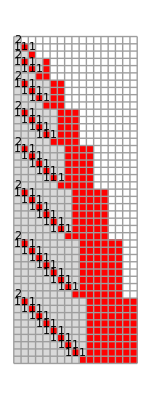


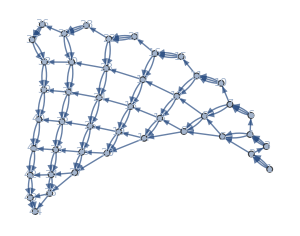
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,NetSize->300]
```

```mathematica
SSS[rs:{___Rule},init_String,n_Integer?Positive,opts___] := Module[{sss},
sss=SSSInitialize[rs,init,Mode->Silent];
If[sss["Verdict"]=!="Dead", 
sss=SSSEvolve[sss,n-1,Sequence@@FilterRules[{opts},Options[SSSEvolve]]]; 
Print@SSSDisplay[sss,Sequence@@FilterRules[{opts},Options[SSSDisplay]]];
];
sss
];
Options[SSS]=Join[Options[SSSEvolve],Options[SSSDisplay]];
SyntaxInformation[SSS]={"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};
```

```mathematica
SSS::usage="SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(Returns a copy of the SSS that can then be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly, looking at its keys, \"Evolution\" and \"Net\", etc.)";
```

```mathematica
Clear[SSSInteractiveDisplay,dynamicLabel];

dynamicLabel[lbl_,max_]:=Dynamic[If[Clock[{1,max,1},max]==lbl,Framed[lbl,Background->Green,RoundingRadius->Scaled[.5]],lbl]];

SetAttributes[SSSInteractiveDisplay,HoldFirst];

SSSInteractiveDisplay[sss_] := With[{mxmx=Max[List @@@ Evaluate[sss]["Net"]]},
Manipulate[
If[Head[vl]===List,vp=Automatic];
If[mx<mn,mx=mn+1];
If[sssmx<sssmn,sssmx=sssmn+1];
If[ntmx<ntmn,ntmx=ntmn+1];
args={Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,RulePlacement->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexSize->vs,
VertexLabels->If[vp===Automatic,vl,Placed[vl,vp]],
DirectedEdges->dir};
SSSDisplay[Evaluate[sss],Flatten[args,1]],
Grid[{{
Control[{{hlm,Number,"HighlightMethod"},{Dot,Frame,Number,None}}],
Control[{{sr,Bottom,"RulePlacement"},{Bottom,Top,Left,Right,None}}],
Control[{{nm,GraphPlot,"NetMethod"},{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D,All}}],
Button["Save these options",
CellPrint[ExpressionCell[Defer[SSSDisplay][Defer[sss],Evaluate[Sequence@@args]],"Input"]];
SelectionMove[InputNotebook[],Previous,Cell];
]
}},Spacings->2],
{args,{},ControlType->None},
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],
Row[{
Control[{{dir,False,"directed"},{False,True}}],"    ",
Control[{{no,False,"NoSSS"},{False,True}}]
}]
},
{Control[{{sssmn,0,"SSSMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{sssmx,mxmx+1,"SSSMax"},0,mxmx+1,1,Appearance->"Labeled"}],"(a NetMethod option)"},{Control[{{ntmn,0,"NetMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{ntmx,mxmx+1,"NetMax"},0,mxmx+1,1,Appearance->"Labeled"}],
Control[{{vs,Automatic,"VertexSize →"},{Automatic,Tiny,Small,Medium,Large,0.8->"Huge"},ControlType->PopupMenu}]
},
{Control[{{ssss,220,"SSSSize"},10,500,Appearance->"Labeled"}],
Control[{{is,350,"ImageSize"},10,500,Appearance->"Labeled"}],Control[{{vl,Automatic,"VertexLabels →"},{Automatic,None,"Name","VertexWeight",
((#->Placed[#,Center,Function[{arg},dynamicLabel[arg,ntmx]]])&/@Range[ntmn+1,ntmx-1])->"Dynamic"},ControlType->PopupMenu}]},
{Control[{{cns,20,"IconSize"},10,50,Appearance->"Labeled"}],Control[{{ns,300,"NetSize"},10,800,Appearance->"Labeled"}],
Control[{{vp,Automatic,"Placed"},
{Automatic,Center,Before,After,Below,Above,Tooltip,StatusArea}}]}
},Alignment->Right,Spacings->2]
]]
SSSInteractiveDisplay::usage="SSSInteractiveDisplay[sss] provides an interactive display of sss and its causal network, with controls for easy adjustment of common options.  Click the button to create a SSSDisplay object with the selected options.";
```

If everything above loaded correctly, the following lines will work:

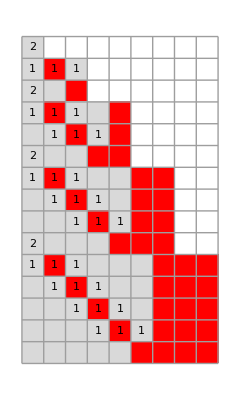
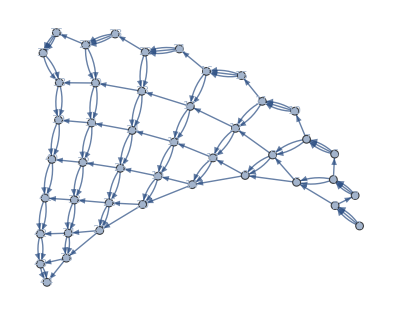
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15,NetMethod->GraphPlot];
```

```mathematica
SSSInteractiveDisplay[sss]
```

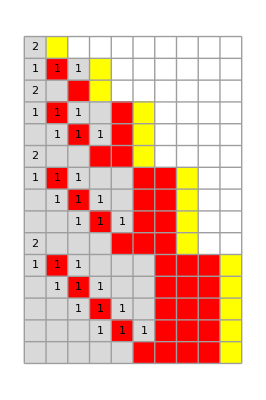
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2=SSS[{"ABA"->"AAB","A"->"ABA"}, "AC",44,SSSMax->15,NetMethod->GraphPlot];
```

```mathematica
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB}

```mathematica
sss2["Evolution"]
```

{AC,ABAC,AABC,ABAABC,AABABC,AAABBC,ABAAABBC,AABAABBC,AAABABBC,AAAABBBC,ABAAAABBBC,AABAAABBBC,AAABAABBBC,AAAABABBBC,AAAAABBBBC,ABAAAAABBBBC,AABAAAABBBBC,AAABAAABBBBC,AAAABAABBBBC,AAAAABABBBBC,AAAAAABBBBBC,ABAAAAAABBBBBC,AABAAAAABBBBBC,AAABAAAABBBBBC,AAAABAAABBBBBC,AAAAABAABBBBBC,AAAAAABABBBBBC,AAAAAAABBBBBBC,ABAAAAAAABBBBBBC,AABAAAAAABBBBBBC,AAABAAAAABBBBBBC,AAAABAAAABBBBBBC,AAAAABAAABBBBBBC,AAAAAABAABBBBBBC,AAAAAAABABBBBBBC,AAAAAAAABBBBBBBC,ABAAAAAAAABBBBBBBC,AABAAAAAAABBBBBBBC,AAABAAAAAABBBBBBBC,AAAABAAAAABBBBBBBC,AAAAABAAAABBBBBBBC,AAAAAABAAABBBBBBBC,AAAAAAABAABBBBBBBC,AAAAAAAABABBBBBBBC,AAAAAAAAABBBBBBBBC}